# Bacterial chemotaxis-like ORN adaptation model

## Bacterial chemotaxis

```mathematica
Step[t_,t0_,τ_]=(Tanh[(t-t0)/τ]+1)/2;
Pulse[t_,t0_,tlen_,τ_]=Step[t,t0,τ](1-Step[t,t0+tlen,τ]);
Signal[t_,Sbackground_,Samplitude_,tStart_,tDuration_,tSharp_]=Sbackground +Samplitude Pulse[t,tStart,tDuration,tSharp];
```

```mathematica
eq={M'[t]==α(1-A[t])-β A[t],τ F'[t]+F[t]==e0+e1 M[t] + n Log[(1+OO[t]/Ki)/(1+OO[t]/Ka)],A[t]==(1+ⅇ^F[t])^-1};
init={M[0]==0,F[0]==e0};
par={Ka->3000,Ki->18,α->2,β->4,τ->0.2,A0->0.2,e0->6,e1->-1,n->2,tStart->20,tDuration->5,tSharp->0.1,tMax->30};
eqs=Join[eq/.par/.OO[t]->Signal[t,Sbackground,Samplitude,tStart,tDuration,tSharp]/.par,init/.par/.OO[0]->Signal[0,Sbackground,Samplitude,tStart,tDuration,tSharp]/.par];
```

```mathematica
sol=ParametricNDSolveValue[eqs,{M,A,F},{t,0,(tMax/.par)},{Sbackground,Samplitude},Method->"Automatic",MaxSteps->10^6];
```

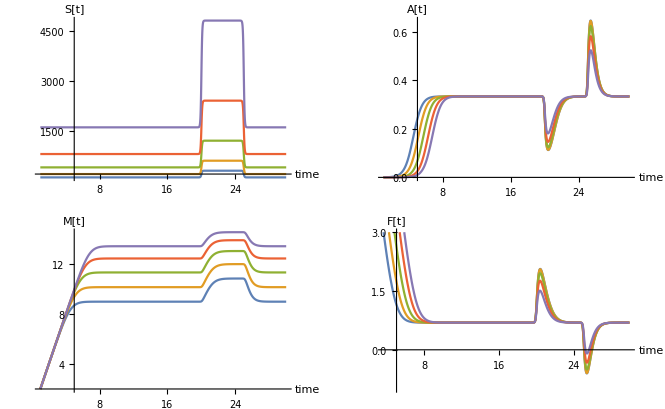

```mathematica
factors={1,2,4,8,16};
GraphicsGrid[{{Plot[Evaluate[Table[Signal[t,S0,2S0,tStart,tDuration,tSharp]/.par,{S0,factors 100}]],{t,1,tMax/.par},PlotRange->{All,All},AxesLabel->{"time","S[t]"}],
Plot[Evaluate[Table[sol[S0,2 S0][[2]][t],{S0,factors 100}]],{t,1,tMax/.par},PlotRange->{All,All},AxesLabel->{"time","A[t]"}]},
{Plot[Evaluate[Table[sol[S0,2 S0][[1]][t],{S0,factors 100}]],{t,1,tMax/.par},PlotRange->{All,All},AxesLabel->{"time","M[t]"}],
Plot[Evaluate[Table[sol[S0,2 S0][[3]][t],{S0,factors 100}]],{t,1,tMax/.par},PlotRange->{All,{-1,3}},AxesLabel->{"time","F[t]"}]}}]
```